```mathematica
(* PŘÍKLAD 1 - žlutá LED *)
ClearAll["Global`*"]
U1 = 5;
UD1=2;
ID1 = 20*10^-3;

UR1 = U1-UD1;
R1=UR1/ID1;

Print["Ubytek napeti na R1 je UR1 = ",UR1," V."]
Print["Minimální hodnota odporu R1 je R1 = ",R1," Ω."]
```

Ubytek napeti na R1 je UR1 = 3 V.

Minimální hodnota odporu R1 je R1 = 150 Ω.

```mathematica
(* PŘÍKLAD 1 - zelená LED *)
ClearAll["Global`*"]
U1 = 9;
UD1=2.5;
ID1 = 25*10^-3;

UR1 = U1-UD1;
R1=UR1/ID1;

Print["Ubytek napeti na R1 je UR1 = ",UR1," V."]
Print["Minimální hodnota odporu R1 je R1 = ",R1," Ω."]
```

Ubytek napeti na R1 je UR1 = 6.5 V.

Minimální hodnota odporu R1 je R1 = 260. Ω.

```mathematica
(* PŘÍKLAD 1 - modrá LED *)
ClearAll["Global`*"]
U1 = 5;
UD1=3.5;
ID1 = 30*10^-3;

UR1 = U1-UD1;
R1=UR1/ID1;

Print["Ubytek napeti na R1 je UR1 = ",UR1," V."]
Print["Minimální hodnota odporu R1 je R1 = ",R1," Ω."]
```

Ubytek napeti na R1 je UR1 = 1.5 V.

Minimální hodnota odporu R1 je R1 = 50. Ω.

```mathematica
(* PŘÍKLAD 2 - žlutá LED *)
ClearAll["Global`*"]
R1 = 330;
UD1 = 2;
ID1 = 20.*10^-3;

UR1 = R1*ID1;
U1 = UR1+UD1;

Print["Ubytek napeti na R1 je UR1 = ",UR1," V."]
Print["Maximální hodnota zdroje U1 = ",U1," V."]
```

Ubytek napeti na R1 je UR1 = 6.6 V.

Maximální hodnota zdroje U1 = 8.6 V.

```mathematica
(* PŘÍKLAD 2 - zelená LED *)
ClearAll["Global`*"]
R1 = 220;
UD1 = 2.5;
ID1 = 25.*10^-3;

UR1 = R1*ID1;
U1 = UR1+UD1;

Print["Ubytek napeti na R1 je UR1 = ",UR1," V."]
Print["Maximální hodnota zdroje U1 = ",U1," V."]
```

Ubytek napeti na R1 je UR1 = 5.5 V.

Maximální hodnota zdroje U1 = 8. V.

```mathematica
(* PŘÍKLAD 2 - modrá LED *)
ClearAll["Global`*"]
R1 = 150;
UD1 = 3.5;
ID1 = 30.*10^-3;

UR1 = R1*ID1;
U1 = UR1+UD1;

Print["Ubytek napeti na R1 je UR1 = ",UR1," V."]
Print["Maximální hodnota zdroje U1 = ",U1," V."]
```

Ubytek napeti na R1 je UR1 = 4.5 V.

Maximální hodnota zdroje U1 = 8. V.

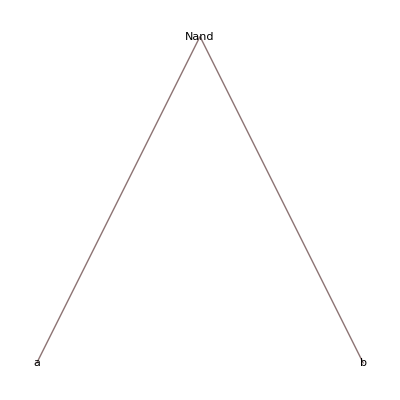

```mathematica
(* LOGICKÉ SCHÉMA *)
-Graphics-;
y = Nand[a,b]// TreeForm
```

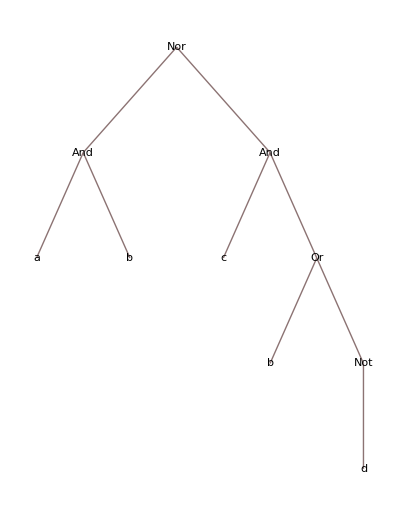

```mathematica
y = Nor[And[a,b],And[c,Or[b,Not[d]]]]//TreeForm
```